```mathematica
δall[V__]:=
Module[
{ee={10^-10,10^-5,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1},δ50Lepage={-0.000421343353,-0.133227246,-1.319383451,-0.900186195,-0.146570028,-0.654835316,1.232867297,-0.579619620,-1.156444634,-0.106466466,-1.457426179,1.160634967},α=2.,u0=1.*10^-10,
k,sol,δs,δr,r2,δr1=Range@12,graph=Range@12,en},
r2=u0;nV=Length[V];k:=√(2en);
Print[ee];
(*Print[V];*)
Table[
Print[ee[[i]]];
en=ee[[i]];
PrintTemporary[en];
δr1[[i]]=Map[First@Reap[Table[
sol=Flatten[NDSolve[{u''[r]+α(en-#[r])u[r]==0,u'[r2]==1,u[r2]==u0},u,{r,r1,r2},AccuracyGoal->20,PrecisionGoal->10,WorkingPrecision->50, MaxSteps->Infinity,InterpolationOrder->All,Method->{"Shooting","StartingInitialConditions"->{u[r2]==u0,u'[r2]==1}}]];
δs=FindRoot[u'[r1]/u[r1]==(k+1/(k r1)) Cot[k r1+δ+Log[2 k r1]/k]/.sol,{δ,-1.3},WorkingPrecision->20];
δr=δ/.δs;
δr=NestWhile[Sign[#](Abs[#]-π)&,δr,Abs[#]>π/2&];
(*Print[{r1,δr}];*)
Sow[{r1,δr}],{r1,1,200,1}]]&,V];
(*Print[δr1[[i]]];*)
graph[[i]]=ListPlot[δr1[[i]],Joined->True,ImageSize->Large,PlotLabel->(#[r])&/@V];
PrintTemporary[e,"Done"];
Print[graph[[i]]],{i,1,12}]
graph
]
```

{1/10000000000,1/100000,0.001,0.003,0.007,0.01,0.03,0.07,0.1,0.3,0.7,1}

1/10000000000

NDSolve::precw: 参数函数的精度 ({{2. (1/10000000000+1.38622 Power[«2»]) u[r]+u''[r]==0,u'[1.×10^-10]==1,u[1.×10^-10]==1.×10^-10},{},{},{},{}}) 小于 WorkingPrecision (50.).

General::stop: 在本次计算中，NDSolve::precw 的进一步输出将被抑制.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法找到 merit 函数的充足的降低. 您可能需要多于 20. 位工作精度以满足这些容差.

General::stop: 在本次计算中，FindRoot::lstol 的进一步输出将被抑制.

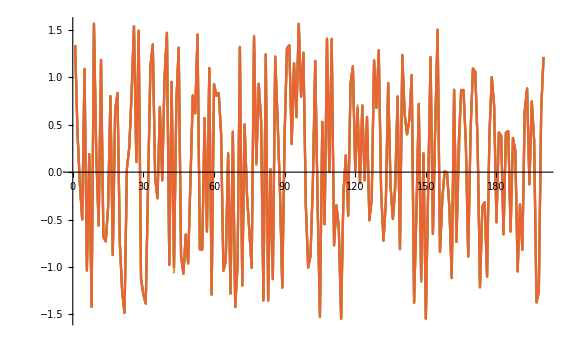

1/100000

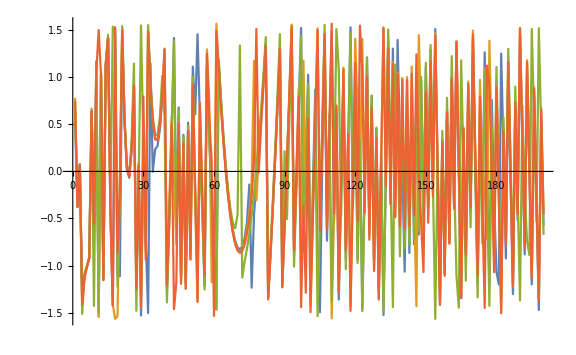

0.001

FindRoot::precw: 参数函数的精度 (36.2155820044763820489029673333934400276619304488==-22.4054 Cot[53.9375-δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (0.4047197897713266566456629457417432330038539013587==-11.2251 Cot[38.3935-δ]) 小于 WorkingPrecision (20.).

FindRoot::precw: 参数函数的精度 (-0.621870045263358644131072413033974522082677142064==-7.49828 Cot[29.2823-δ]) 小于 WorkingPrecision (20.).

General::stop: 在本次计算中，FindRoot::precw 的进一步输出将被抑制.

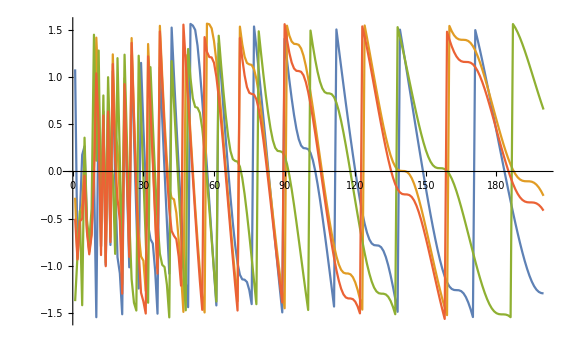

0.003

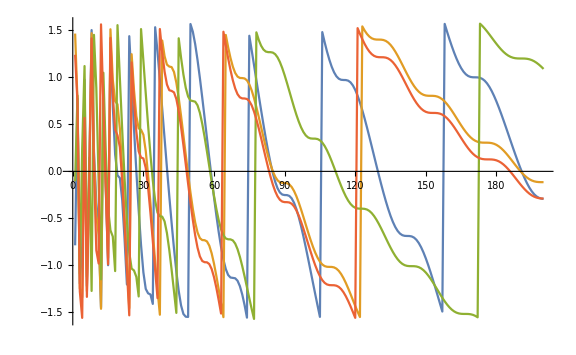

0.007

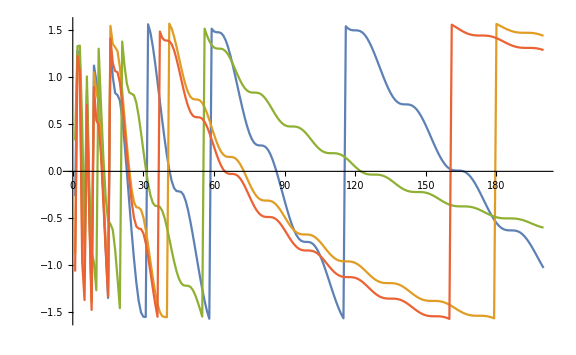

0.01

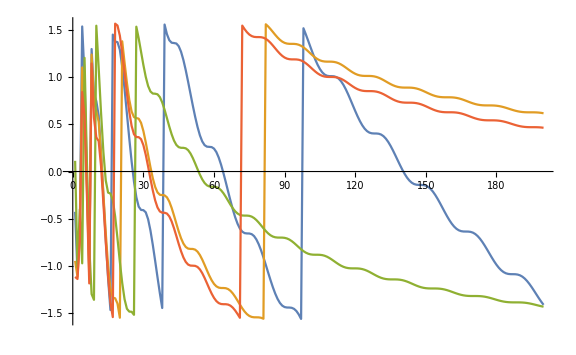

0.03

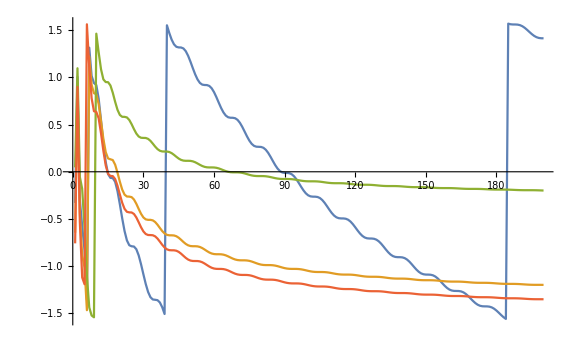

0.07

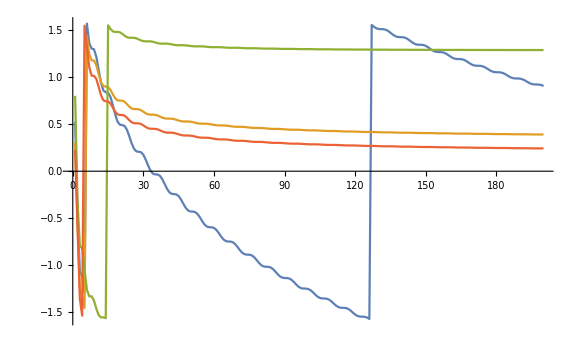

0.1

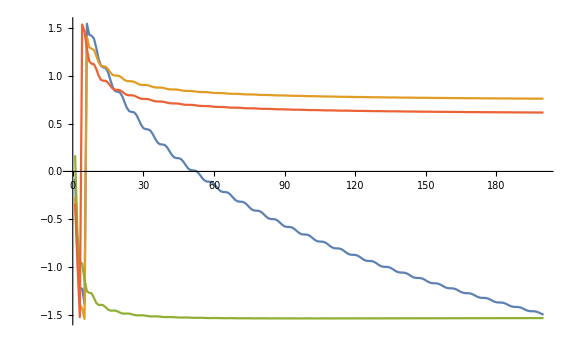

0.3

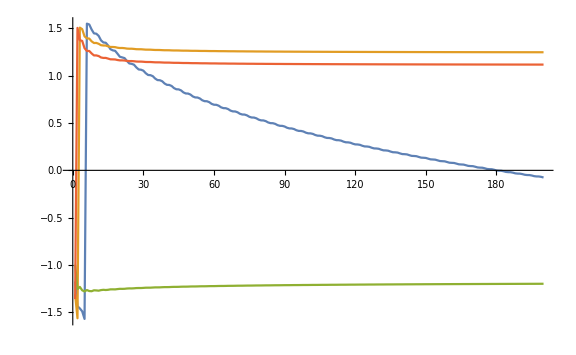

0.7

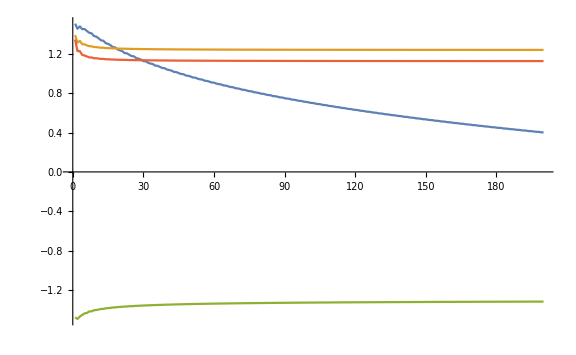

1

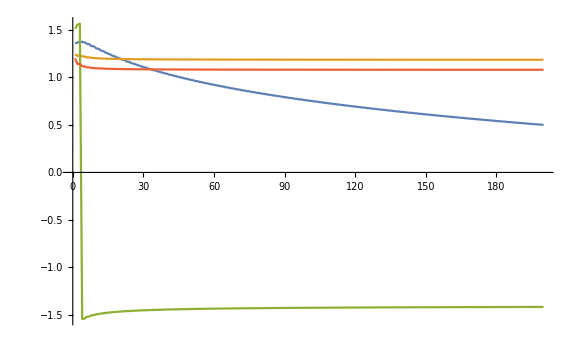

{Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-,Null -Graphics-}

```mathematica
δall[{-1.3862179318475605/#^1.2152447118079408&,-1/#-(1.0415223038416566 ⅇ^(-0.9990999998788636#))/#&,-0.39300593613292306/#^1.5993730406518318-1/#&,-1/#-(0.7938946124458129 ⅇ^(-0.7393687788904056 #^2))/#&}]
```